### Curva de carga capacitor t = tiempo [s] r = resistencia [Ω] c = capacitor [F] vf = tensión de fuente [V]

```mathematica
v[t_,r_,c_,vf_:1]:=vf(1-E^(-t/(r*c)))
```

### Aplicación sobre circuito

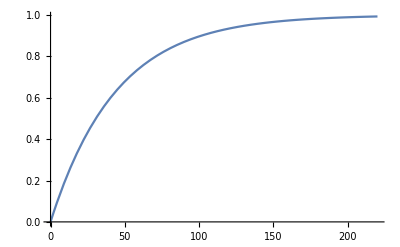

```mathematica
res=220 10^3 2;
cap=100 10^-6;
vt[t_]:=v[t,res,cap]
Plot[vt[t],{t,0,res*cap*5}]
```

### Despeje tiempo de carga a tensión objetivo Tensión objetivo = 5v

```mathematica
t[v_,r_,c_,vf_:1]:=c*r*Log[vf/(vf-v)]
```

```mathematica
With[{tsol=t[vo,r 10^3,c 10^-6,vf],tmax=t[vf*0.99,r 10^3,c 10^-6,vf]*1.1},
Manipulate[
Plot[t[v,r 10^3,c 10^-6,vf],{v,0,vf},PlotRange->{{0,tmax}},Epilog->{
Line[{{0,tsol},{vo,tsol}}],Line[{{vo,0},{vo,tsol}}],
Text[N[tsol,2],{vo+0.5,tsol+0.5}]}],
{{vf,220,"Tensión final [v]"},0.1,220,1},
{{vo,5,"Tensión objetivo [v]"},0.1,vf*0.99,vf/100},
{{r,res 10^-3,"Resistencia [kΩ]"},1,1000,10},
{{c,cap 10^6, "Capacitor [μF]"},1,1000,10}]
]
```

```mathematica
t[5,res,cap,220]//N
```

1.01154